```mathematica
β[x_,ξ_]:=√(1-ξ^-1 4 x/(1-x))
xmax[ξ_]:=1/(1+4/ξ)
C2g[x_,ξ_]:=4 TR/(4π)(Log[(1+β[x,ξ])/(1-β[x,ξ])](-8 x^2 ξ^-2-4x ξ^-1(3x-1)+(2 x^2-2x+1))+β[x,ξ](4 ξ^-1 x(x-1)-(8 x^2-8x+1)))
CLg[x_,ξ_]:=16 TR/(4π)(x(1-x)β[x,ξ] - 2x ξ^-1 Log[(1+β[x,ξ])/(1-β[x,ξ])])
Pgq[x_]:= 2 CF/(4π) (2/x−2+x)
Pggloc[nf_]:=(CA 11/3-2/3 nf)1/(4π)
Pggsing[x_]:= (4CA)/(4π) 1/(1-x)
Pggreg[x_]:=(4CA)/(4π)(1/x-2+x-x^2)
β0[nf_]:=1/(4π)(11/3 CA-2/3 nf)
```

```mathematica
(*Integrate[C2g[z,ξ]Pgq[x/z],{z,x,xmax[ξ]},Assumptions->0<x<xmax[ξ]]*)
```

```mathematica
C2q21[x_,ξ_]:=NIntegrate[1/z C2g[z,ξ]Pgq[x/z]/.{CF->4/3,TR->1/2},{z,x,xmax[ξ]}]
C2q21NEW[x_,ξ_]:=1/x NIntegrate[1/z z C2g[z,ξ]Pgq[x/z]/.{CF->4/3,TR->1/2},{z,x,xmax[ξ]}]
CLq21[x_,ξ_]:=NIntegrate[1/z CLg[z,ξ]Pgq[x/z]/.{CF->4/3,TR->1/2},{z,x,xmax[ξ]}]
CLq21NEW[x_,ξ_]:=1/x NIntegrate[1/z z CLg[z,ξ]Pgq[x/z]/.{CF->4/3,TR->1/2},{z,x,xmax[ξ]}]
```

```mathematica
C2g21reg[x_,ξ_]:=NIntegrate[1/z C2g[z,ξ]Pggreg[x/z]/.{CA->3,CF->4/3,TR->1/2},{z,x,xmax[ξ]}]
C2g21loc[x_,ξ_,nf_]:=N[C2g[x,ξ]Pggloc[nf]/.{CA->3,CF->4/3,TR->1/2}]
C2g21sing[x_,ξ_]:=NIntegrate[Pggsing[z](1/z C2g[x/z,ξ]-C2g[x,ξ])/.{CA->3,CF->4/3,TR->1/2},{z,x/xmax[ξ],1}] - N[C2g[x,ξ]/.TR->1/2]NIntegrate[Pggsing[z]/.{CA->3,CF->4/3,TR->1/2},{z,0,x}]
C2g21[x_,ξ_,nf_]:=(C2g21reg[x,ξ]+C2g21loc[x,ξ,nf]+C2g21sing[x,ξ])-N[β0[nf] C2g[x,ξ]/.{CA->3,CF->4/3,TR->1/2}]
C2g21NEW[x_,ξ_]:=C2g21reg[x,ξ]+C2g21sing[x,ξ]
```

```mathematica
CLg21reg[x_,ξ_]:=NIntegrate[1/z CLg[z,ξ]Pggreg[x/z]/.{CA->3,CF->4/3,TR->1/2},{z,x,xmax[ξ]}]
CLg21loc[x_,ξ_,nf_]:=N[CLg[x,ξ]Pggloc[nf]/.{CA->3,CF->4/3,TR->1/2}]
CLg21sing[x_,ξ_]:=NIntegrate[Pggsing[z](1/z CLg[x/z,ξ]-CLg[x,ξ])/.{CA->3,CF->4/3,TR->1/2},{z,x/xmax[ξ],1}] - N[CLg[x,ξ]/.TR->1/2]NIntegrate[Pggsing[z]/.{CA->3,CF->4/3,TR->1/2},{z,0,x}]
CLg21[x_,ξ_,nf_]:=(CLg21reg[x,ξ]+CLg21loc[x,ξ,nf]+CLg21sing[x,ξ])-N[β0[nf] CLg[x,ξ]/.{CA->3,CF->4/3,TR->1/2}]
```

```mathematica
N[C2g21[0.1,2,4]]
```

0.918969

```mathematica
C2q21[0.01,2]
```

0.237192

0.109963

0.208999

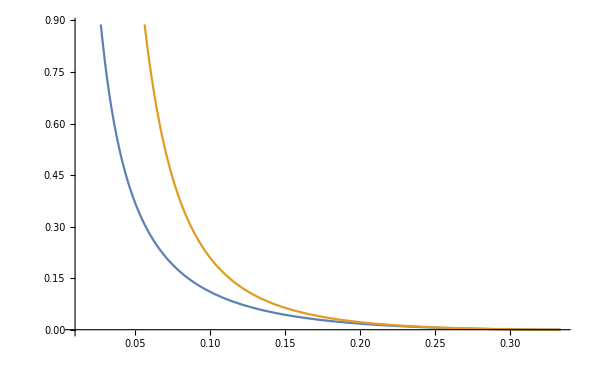

```mathematica
N[C2q21[0.1,2]]
N[C2q21NEW[0.1,2]]
Plot[{C2q21[x,2],C2q21NEW[x,2]},{x,0.01,xmax[2]}]
```

-0.0804944

-0.172104

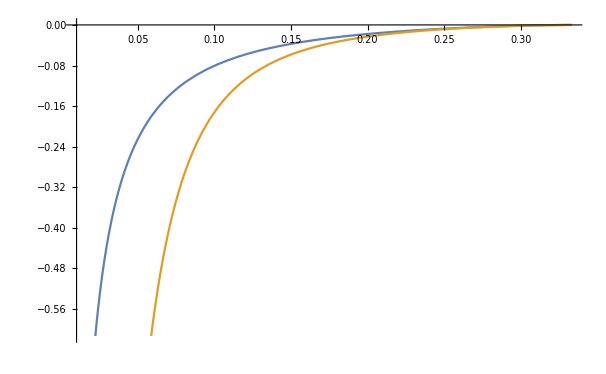

```mathematica
N[CLq21[0.1,2]]
N[CLq21NEW[0.1,2]]
Plot[{CLq21[x,2],CLq21NEW[x,2]},{x,0.01,xmax[2]}]
```

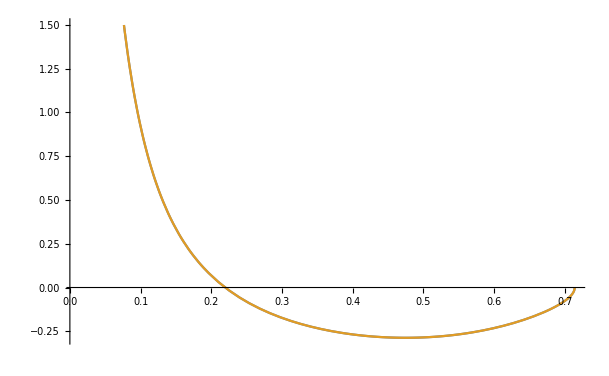

```mathematica
Plot[{C2g21[x,10,4],C2g21NEW[x,10]},{x,0.01,xmax[10]}]
```

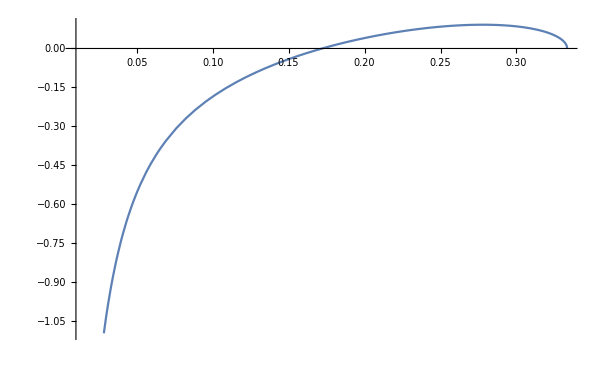

```mathematica
Plot[CLg21[x,2,4],{x,0.01,xmax[2]}]
```

```mathematica
Import["/Users/niccololaurenti/Master-thesis/mu_dep_parts/xi=2.dat"]
```

{{0.001,-84.8432},{0.002,-40.9914},{0.003,-26.5192},{0.004,-19.3405},{0.005,-15.0682},{0.006,-12.2486},{0.007,-10.2473},{0.008,-8.75968},{0.009,-7.61044},{0.01,-6.69733},{0.011,-5.95705},{0.012,-5.34473},{0.013,-4.82958},{0.014,-4.39071},{0.015,-4.01275},{0.016,-3.68491},{0.017,-3.39729},{0.018,-3.14307},{0.019,-2.9169},{0.02,-2.71453},{0.021,-2.53251},{0.022,-2.36813},{0.023,-2.2191},{0.024,-2.08321},{0.025,-1.95886},{0.026,-1.84469},{0.027,-1.73954},{0.028,-1.64242},{0.029,-1.55247},{0.03,-1.46897},{0.031,-1.39126},{0.032,-1.31877},{0.033,-1.25103},{0.034,-1.1876},{0.035,-1.12811},{0.036,-1.0722},{0.037,-1.01958},{0.038,-0.969984},{0.039,-0.923157},{0.04,-0.878886},{0.041,-0.836975},{0.042,-0.797246},{0.043,-0.759539},{0.044,-0.723594},{0.045,-0.689322},{0.046,-0.656714},{0.047,-0.625657},{0.048,-0.596047},{0.049,-0.567787},{0.05,-0.540791},{0.051,-0.514979},{0.052,-0.490276},{0.053,-0.466615},{0.054,-0.443933},{0.055,-0.422171},{0.056,-0.401277},{0.057,-0.381201},{0.058,-0.361896},{0.059,-0.343319},{0.06,-0.325432},{0.061,-0.307875},{0.062,-0.290933},{0.063,-0.274629},{0.064,-0.258927},{0.065,-0.243796},{0.066,-0.229207},{0.067,-0.215132},{0.068,-0.201544},{0.069,-0.188419},{0.07,-0.175734},{0.071,-0.163468},{0.072,-0.151601},{0.073,-0.140113},{0.074,-0.128986},{0.075,-0.118204},{0.076,-0.107751},{0.077,-0.0976117},{0.078,-0.0877722},{0.079,-0.078219},{0.08,-0.0689396},{0.081,-0.0599219},{0.082,-0.0508737},{0.083,-0.0419125},{0.084,-0.0332341},{0.085,-0.024826},{0.086,-0.0166763},{0.087,-0.00877382},{0.088,-0.00110787},{0.089,0.00633164},{0.09,0.0135543},{0.091,0.0205692},{0.092,0.0273849},{0.093,0.0340097},{0.094,0.0404515},{0.095,0.0467175},{0.096,0.0528149},{0.097,0.0587505},{0.098,0.0645306},{0.099,0.0701614},{0.1,0.0756486},{0.101,0.0809979},{0.102,0.0862146},{0.103,0.0913038},{0.104,0.0962702},{0.105,0.101119},{0.106,0.105853},{0.107,0.110479},{0.108,0.1153},{0.109,0.120085},{0.11,0.124734},{0.111,0.129254},{0.112,0.13365},{0.113,0.137925},{0.114,0.142085},{0.115,0.146133},{0.116,0.150073},{0.117,0.15391},{0.118,0.157647},{0.119,0.161287},{0.12,0.164834},{0.121,0.168291},{0.122,0.171662},{0.123,0.174948},{0.124,0.178154},{0.125,0.181282},{0.126,0.184335},{0.127,0.187315},{0.128,0.190224},{0.129,0.193065},{0.13,0.195841},{0.131,0.198552},{0.132,0.201203},{0.133,0.203794},{0.134,0.206328},{0.135,0.208806},{0.136,0.21123},{0.137,0.213655},{0.138,0.216259},{0.139,0.21879},{0.14,0.221251},{0.141,0.223644},{0.142,0.225972},{0.143,0.228235},{0.144,0.230437},{0.145,0.232578},{0.146,0.234661},{0.147,0.236688},{0.148,0.238659},{0.149,0.240577},{0.15,0.242443},{0.151,0.244259},{0.152,0.246026},{0.153,0.247745},{0.154,0.249417},{0.155,0.251045},{0.156,0.252629},{0.157,0.25417},{0.158,0.25567},{0.159,0.257129},{0.16,0.258549},{0.161,0.259931},{0.162,0.261275},{0.163,0.262583},{0.164,0.263856},{0.165,0.265095},{0.166,0.266299},{0.167,0.267471},{0.168,0.268611},{0.169,0.269781},{0.17,0.270968},{0.171,0.272117},{0.172,0.273229},{0.173,0.274304},{0.174,0.275343},{0.175,0.276347},{0.176,0.277317},{0.177,0.278253},{0.178,0.279156},{0.179,0.280027},{0.18,0.280866},{0.181,0.281673},{0.182,0.28245},{0.183,0.283198},{0.184,0.283915},{0.185,0.284604},{0.186,0.285264},{0.187,0.285895},{0.188,0.2865},{0.189,0.287077},{0.19,0.287627},{0.191,0.288151},{0.192,0.288648},{0.193,0.28912},{0.194,0.289566},{0.195,0.289988},{0.196,0.290384},{0.197,0.290756},{0.198,0.291103},{0.199,0.291426},{0.2,0.291726},{0.201,0.291919},{0.202,0.292096},{0.203,0.292255},{0.204,0.292397},{0.205,0.292521},{0.206,0.292629},{0.207,0.292719},{0.208,0.292792},{0.209,0.292849},{0.21,0.292888},{0.211,0.292911},{0.212,0.292916},{0.213,0.292905},{0.214,0.292876},{0.215,0.29283},{0.216,0.292767},{0.217,0.292687},{0.218,0.292589},{0.219,0.292473},{0.22,0.29234},{0.221,0.292189},{0.222,0.292021},{0.223,0.291833},{0.224,0.291628},{0.225,0.291404},{0.226,0.291161},{0.227,0.290899},{0.228,0.290617},{0.229,0.290316},{0.23,0.289863},{0.231,0.289363},{0.232,0.288857},{0.233,0.288342},{0.234,0.28782},{0.235,0.287289},{0.236,0.286749},{0.237,0.286201},{0.238,0.285642},{0.239,0.285074},{0.24,0.284495},{0.241,0.283905},{0.242,0.283304},{0.243,0.282691},{0.244,0.282065},{0.245,0.281426},{0.246,0.280773},{0.247,0.280106},{0.248,0.279424},{0.249,0.278726},{0.25,0.278012},{0.251,0.277281},{0.252,0.276532},{0.253,0.275765},{0.254,0.274978},{0.255,0.274078},{0.256,0.27305},{0.257,0.272019},{0.258,0.270984},{0.259,0.269944},{0.26,0.2689},{0.261,0.267849},{0.262,0.266791},{0.263,0.265725},{0.264,0.264651},{0.265,0.263567},{0.266,0.262472},{0.267,0.261366},{0.268,0.260247},{0.269,0.259114},{0.27,0.257966},{0.271,0.256801},{0.272,0.255619},{0.273,0.254419},{0.274,0.253198},{0.275,0.251955},{0.276,0.250557},{0.277,0.249096},{0.278,0.24763},{0.279,0.246156},{0.28,0.244673},{0.281,0.243181},{0.282,0.241678},{0.283,0.240162},{0.284,0.238631},{0.285,0.237085},{0.286,0.235521},{0.287,0.233937},{0.288,0.232332},{0.289,0.230703},{0.29,0.229048},{0.291,0.227365},{0.292,0.225582},{0.293,0.223717},{0.294,0.221835},{0.295,0.219933},{0.296,0.218009},{0.297,0.216061},{0.298,0.214085},{0.299,0.21208},{0.3,0.210041},{0.301,0.207967},{0.302,0.205852},{0.303,0.203694},{0.304,0.201462},{0.305,0.199141},{0.306,0.196778},{0.307,0.194366},{0.308,0.191902},{0.309,0.18938},{0.31,0.186796},{0.311,0.184142},{0.312,0.181413},{0.313,0.178595},{0.314,0.175683},{0.315,0.172672},{0.316,0.169552},{0.317,0.166311},{0.318,0.162936},{0.319,0.159421},{0.32,0.155773},{0.321,0.151919},{0.322,0.147833},{0.323,0.143483},{0.324,0.138881},{0.325,0.133915},{0.326,0.128484},{0.327,0.122565},{0.328,0.115931},{0.329,0.108338},{0.33,0.099349},{0.331,0.0882259},{0.332,0.072892},{0.333,0.0443708}}